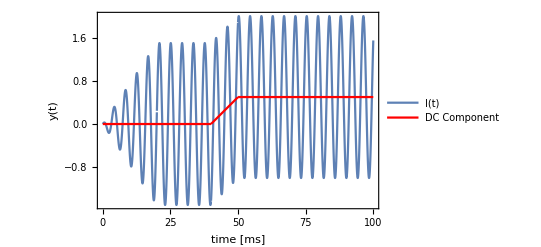

Fig1a.png

```mathematica
(*Example of input current*)
ω = 1.5;
ρ = 1;
I0 = 0.5;
δ = 0.05;
λ = 0.05;
Δ = 20;

g1=Plot[{Which[t<=ρ/δ,t δ ω Cos[ω t],t<=ρ/δ+Δ,ρ ω Cos[ω t],t<=ρ/δ+Δ+ I0/λ,(t-ρ/δ-Δ)λ+ρ ω Cos[ω t],True,I0+ρ ω Cos[ω t]],Which[t<=ρ/δ,0,t<=ρ/δ+Δ,0,t<=ρ/δ+Δ+ I0/λ,(t-ρ/δ-Δ)λ,True,I0]},{t,0,100},PlotStyle->{Default,Red},PlotPoints->4000,MaxRecursion->2,Frame -> True,FrameLabel -> {"time [ms]", "y(t)"},PlotLegends->{"I(t)","DC Component"}]
Export["Fig1a.png",g1]
```